# Coupling with adjustable torsional stiffness

## Reminder1

-Graphics--Graphics-

-Graphics--Graphics-

## Reminder2

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## PROJECT

## Elastic Constant

-Graphics-

```mathematica
eq1=Ra+Rb-m g-M g==0
```

-g m-g M+Ra+Rb==0

```mathematica
eq2=M g posizione-Rb L+m g L/2==0
```

(g L m)/2+g M posizione-L Rb==0

```mathematica
solF=Solve[{eq1,eq2},{Rb,Ra}][[1]]
```

{Rb→-(-g L m-2 g M posizione)/(2 L),Ra→-(-g L m-2 g L M+2 g M posizione)/(2 L)}

## Azioni interne

### Ty

#### da x a L

```mathematica
Ty1=-Rb+m/L g (L-z)/.solF
```

(-g L m-2 g M posizione)/(2 L)+(g m (L-z))/L

#### da 0 a x

```mathematica
Ty2=-Rb+m/L g (L-z)+M g/.solF
```

g M+(-g L m-2 g M posizione)/(2 L)+(g m (L-z))/L

#### Plot

```mathematica
fT=Piecewise[{{(Ty2/.posizione->position), z<=position}, {(Ty1/.posizione->position), z>position}}]
```

Piecewise[{{g M+(-g L m-2 g M position)/(2 L)+(g m (L-z))/L, z≤position}, {(-g L m-2 g M position)/(2 L)+(g m (L-z))/L, z>position}, {0, True}}]

```mathematica
Manipulate[Block[{g=9.81,m=5,M=15,L=2},
Plot[Piecewise[{{(Ty2/.posizione->position), z<position}, {(Ty1/.posizione->position), z>position}}],{z,0,L},PlotStyle->Thick,PlotRange->{{0,L},{-200,200}}]
],{position,0,2}]
```

### Mx

#### da x a L

```mathematica
Mx1=Integrate[Ty1,z, GeneratedParameters->C]
```

1/2 g (m z-(2 M posizione z)/L-(m z^2)/L)+C[1]

```mathematica
c=Solve[(Mx1/.z->L)==0][[1]]
```

{C[1]→g M posizione}

```mathematica
Collect[Simplify[Mx1/.c],posizione]
```

(g M posizione (L-z))/L+(g m (L-z) z)/(2 L)

#### da 0 a x

```mathematica
Mx2=Integrate[Ty2,z, GeneratedParameters->C]
```

1/2 g (m z+2 M z-(2 M posizione z)/L-(m z^2)/L)+C[1]

```mathematica
c2=Solve[(Mx2/.z->0)==0][[1]]
```

{C[1]→0}

```mathematica
Collect[Simplify[Mx2/.c2],posizione]
```

-(g M posizione z)/L+(g z (L (m+2 M)-m z))/(2 L)

#### Plot

```mathematica
fM=Piecewise[{{(Mx2/.c2/.posizione->position), z<position}, {(Mx1/.c/.posizione->position), z>=position}}]
```

Piecewise[{{1/2 g (m z+2 M z-(2 M position z)/L-(m z^2)/L), z<position}, {g M position+1/2 g (m z-(2 M position z)/L-(m z^2)/L), z≥position}, {0, True}}]

```mathematica
Manipulate[Block[{g=9.81,m=5,M=15,L=2},
Plot[Piecewise[{{(Mx2/.c2/.posizione->position), z<position}, {(Mx1/.c/.posizione->position), z>position}}],{z,0,L},PlotStyle->Thick,PlotRange->{{0,L},{0,90}}]
],{position,0,2}]
```

we can find the maximum by means of the derivation

```mathematica
Solve[{D[fM,position]==0,D[fM,z]==0},{position,z}]
```

{}

Not finding a stationary point from the derivative of the gradient, we deduce that the maximum is on the edge of the function:

```mathematica
fM
```

Piecewise[{{1/2 g (m z+2 M z-(2 M position z)/L-(m z^2)/L), z<position}, {g M position+1/2 g (m z-(2 M position z)/L-(m z^2)/L), z≥position}, {0, True}}]

```mathematica
fM[[1]][[1]][[1]]/.z->0
```

0

It can’t be

```mathematica
fM[[1]][[2]][[1]]/.z->L
```

0

It can’t be

It must be between the two functions

```mathematica
fM[[1]][[2]][[1]]/.z->position
```

g M position+1/2 g (m position-(m position^2)/L-(2 M position^2)/L)

And its point of minimum is:

```mathematica
Solve[D[fM/.position->z,z]==0,z][[1]]
```

{z→L/2}

## K calculation

### K shaft torsion

M = k teta -> Mz=G teta/L Ip

```mathematica
kbeforeflangeshaft =(G Jshaft)/position;
```

```mathematica
kafterflangeshaft=(G Jshaft)/(L-position);
```

### k beam torsion

```mathematica
kbeforeflangebeam =(G Jbeam)/position;
```

```mathematica
kafterflangebeam =(G Jbeam)/(L-position);
```

### equivalent k

-Graphics-

```mathematica
ex1=I1 teta1''[t]==M[t]-kShaftBefore (teta2[t]-teta1[t])-kBeamBefore(teta2[t]-teta1[t]);
ex2=I2 teta2''[t]==kShaftBefore (teta2[t]-teta1[t])+kBeamBefore(teta2[t]-teta1[t])-kShaftAfter (teta3[t]-teta2[t])-kBeamAfter(teta3[t]-teta2[t]);
ex3=I3 teta3''[t]==kShaftAfter (teta3[t]-teta2[t])+kBeamAfter(teta3[t]-teta2[t]);
```

```mathematica
eqs=LaplaceTransform[{ex1,ex2,ex3},t,s]/.teta1[0]->0/.teta1'[0]->0/.teta2[0]->0/.teta2'[0]->0/.teta3[0]->0/.teta3'[0]->0;
```

```mathematica
sols=Solve[eqs,{LaplaceTransform[teta1[t],t,s],LaplaceTransform[teta2[t],t,s],LaplaceTransform[teta3[t],t,s]}];
```

```mathematica
FdT1=Coefficient[LaplaceTransform[teta1[t],t,s]/.sols,LaplaceTransform[M[t],t,s]][[1]];
FdT2=Coefficient[LaplaceTransform[teta2[t],t,s]/.sols,LaplaceTransform[M[t],t,s]][[1]];
FdT3=Coefficient[LaplaceTransform[teta3[t],t,s]/.sols,LaplaceTransform[M[t],t,s]][[1]];
FdT={FdT1,FdT2,FdT3};
```

```mathematica
poles=Solve[Denominator[FdT]==0,s];
```

```mathematica
zeros=Solve[Numerator[FdT]==0,s];
```

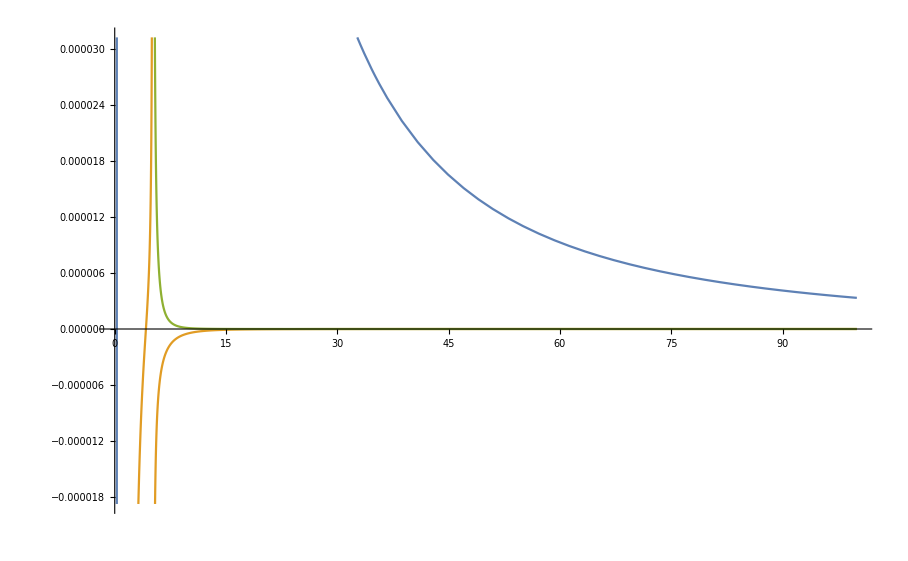

```mathematica
Block[{I3=50,posizione=17,L=20,kBeamAfter=50posizione,kShaftAfter=2 posizione,kShaftBefore=2(L-posizione),kBeamBefore=2(L-posizione),I1=30,I2=100,max=5},Show[
Plot[FdT,{s,0,100}],
ParametricPlot[{(s/.poles[[4]])/I,t},{t,-max,max},PlotStyle->{Dashed,Red}]
]]
```